This does a 2D calculation of the reciprocal frame vectors (two different ways), and plots orthonormal and oblique grids with sample vectors using those bases.

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

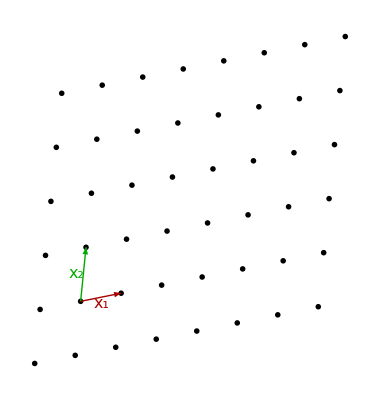

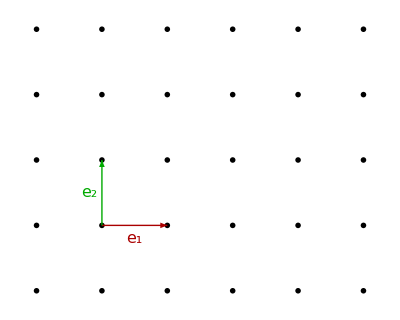

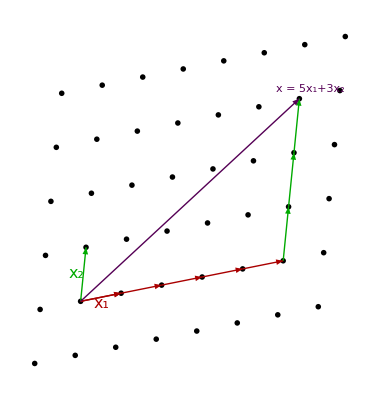

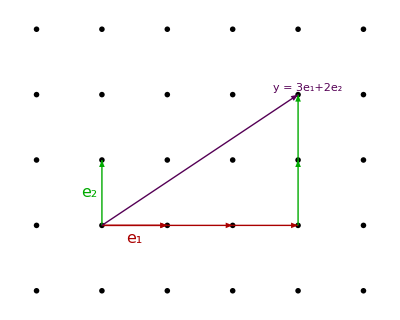

```mathematica
ClearAll[o,f1, f2, g1,g2, e1, e2, bold, fs, sub, super, rot90]

o= {0,0};
e1 = {1,0};
e2 = {0,1};
rot90 = {{0,-1},{1,0}}; (*Active rotation by π/2*)

bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;

f2 = 1.6(e2 + 0.1 e1);
f1 = 1.2(e1 + 0.2 e2);

sub[c_,n_] := Subscript[c// bold, n]//fs;
super[c_,n_] := Superscript[c// bold, n]//fs;

(*computeReciprocal[f1_, f2_] := Module[{g1,g2},

det = Det[{f1, f2}];
g1 = -rot90 . f2 / det;
g2 = rot90 . f1 / det;
{g1, g2}];*)
computeReciprocal[f1_, f2_] := Inverse[{f1,f2}]

(*{g1, g2} = computeReciprocal[f1, f2];*)

(*Graphics[{
Red //Darker,
Arrow[{o,f1}],
Arrow[{o,f2}],

Text[sub["f", 1], f1/2- 0.1 g2/Norm[g2]],
Text[sub["f", 2], f2/2 + 0.1 g1/Norm[g1]],

Green // Darker,
Arrow[{o,g1}],
Arrow[{o,g2}],

Text[super["f", 1], g1/2 - 0.1 f2/Norm[f2]],
Text[super["f", 2], g2/2 - 0.1 f1/Norm[f1]]
}];*)
(*f1
f2
g1
g2
g1. f1
g1. f2
g2 . f1
g2 . f2*)

(* y = L x *)
(*L = {g1,g2}

L.e1
L.e2*)

justgrid[f1_, f2_, c_, s1_, s2_] := Module[{g1,g2},
{g1, g2} = computeReciprocal[f1, f2];
Graphics[{
Black
, PointSize[0.01]
,Table[Point[i f1 + j f2],{i,-1,s1+1}, {j,-1,s2+1}]

, Thick
,Red //Darker
, Arrow[{o,f1}]
,Text[sub[c, 1], f1/2- 0.2 g2/Norm[g2]]

,Green // Darker
, Arrow[{o,f2}]
,Text[sub[c, 2], f2/2 - 0.2 g1/Norm[g1]]
}]
]


plotgrid[f1_, f2_, c_, x_, s1_, s2_] := Module[{r,s, a,g},
r = s1+1;
s = -1;
a = s1 f1 + s2 f2;
g = justgrid[f1,f2,c, s1, s2];
Show[{
g,
Graphics[{
 Thick
,Red //Darker
, Table[ Arrow[{i f1,(i+1)f1}],{i,0,s1-1}]

,Green // Darker
, Table[ Arrow[{s1 f1 + i f2,s1 f1+(i+1)f2}],{i,0,s2-1}]

, Purple // Darker
,Arrow[{o,a}]
,Text[Row[{x //bold // fs, " = " //fs, s1 //fs,sub[c, 1],"+"//fs, s2//fs, sub[c, 2]}], 1.05 a]
}]
}]
]

ClearAll[pfgrid,pegrid]
pfgrid =justgrid[f1,f2,"x", 5, 3]
pegrid = justgrid[e1,e2,"e", 3,2]

ClearAll[pf,pe]
pf = plotgrid[f1,f2,"x", "x", 5, 3]
pe = plotgrid[e1,e2,"e", "y", 3,2]
```

```mathematica
peeters`exportForLatex["fbasisSumFig1", pf] 
peeters`exportForLatex["ebasisSumFig1", pe]
```

{fbasisSumFig1.eps,fbasisSumFig1pn.png}

{ebasisSumFig1.eps,ebasisSumFig1pn.png}

```mathematica
peeters`exportForLatex["fbasisFig1", pfgrid] 
peeters`exportForLatex["ebasisFig1", pegrid]
```

{fbasisFig1.eps,fbasisFig1pn.png}

{ebasisFig1.eps,ebasisFig1pn.png}